```mathematica
(* Finding the ESS of fully random specialisers *)
```

```mathematica
WRand[q_]= Simplify[(1-q)(1-ϵ+ϵ q/l-ϵ q/l/m+ϵ (l-1) QRand/l)]
```

-((-1+q) (l m+(-1+m) q ϵ+l m (-1+QRand) ϵ-m QRand ϵ))/(l m)

```mathematica
Solve[WRand'[q]==0, q]
```

{{q→(-l m-ϵ+m ϵ+l m ϵ+m QRand ϵ-l m QRand ϵ)/(2 (-1+m) ϵ)}}

```mathematica
(* Find q*_FR *)
```

```mathematica
Simplify[Solve[q==(-l m-ϵ+m ϵ+l m ϵ+m q ϵ-l m q ϵ)/(2 (-1+m) ϵ), q]] (* Replace QRand with q *)
```

{{q→(l m (-1+ϵ)+(-1+m) ϵ)/((-2+m+l m) ϵ)}}

```mathematica
(* Finding the invading condition for a fully coordinated founder *)
```

```mathematica
WCordInv[q_]= Simplify[(1-θ)(1-q)(1-ϵ+ϵ q/l+ϵ QRand (l-1)/l)]
```

((-1+q) (l+(q-QRand) ϵ+l (-1+QRand) ϵ) (-1+θ))/l

```mathematica
(* Assuming invader using its optimal q *)
```

```mathematica
Solve[WCordInv'[q]==0, q]
```

{{q→(-l+ϵ+l ϵ+QRand ϵ-l QRand ϵ)/(2 ϵ)}}

```mathematica
(* Get q＾_FCInv *)
```

```mathematica
Simplify[Solve[{q== (-l+ϵ+l ϵ+QRand ϵ-l QRand ϵ)/(2 ϵ), QRand==(l m (-1+ϵ)+(-1+m) ϵ)/((-2+m+l m) ϵ)}, {q, QRand}]]
```

{{q→(l (2+2 m (-1+ϵ)-ϵ)+(-3+2 m) ϵ)/(2 (-2+m+l m) ϵ),QRand→(l m (-1+ϵ)+(-1+m) ϵ)/((-2+m+l m) ϵ)}}

```mathematica
(* Find critical invading conditions *)
```

```mathematica
QRand=(l m (-1+ϵ)+(-1+m) ϵ)/((-2+m+l m) ϵ);Simplify[WCordInv[(l (2+2 m (-1+ϵ)-ϵ)+(-3+2 m) ϵ)/(2 (-2+m+l m) ϵ)]]
```

-((ϵ-l (-2+2 m+ϵ))^2 (-1+θ))/(4 l (-2+m+l m)^2 ϵ)

```mathematica
QRand=(l m (-1+ϵ)+(-1+m) ϵ)/((-2+m+l m) ϵ); Simplify[WRand[(l m (-1+ϵ)+(-1+m) ϵ)/((-2+m+l m) ϵ)]]
```

((-1+m) (-l m+ϵ)^2)/(l m (-2+m+l m)^2 ϵ)

```mathematica
Simplify[Solve[-((ϵ-l (-2+2 m+ϵ))^2 (-1+θ))/(4 l (-2+m+l m)^2 ϵ)==((-1+m) (-l m+ϵ)^2)/(l m (-2+m+l m)^2 ϵ), ϵ]]
```

{{ϵ→(2 (√(-l^2 (-1+m) m (-2+m+l m)^2 (-1+θ))+l (-1+m) m (1+θ)+l^2 m (-1+m+θ-m θ)))/(-4+m (3-2 l (-1+θ)+l^2 (-1+θ)+θ))},{ϵ→-(2 (l^2 (-1+m) m (-1+θ)+√(-l^2 (-1+m) m (-2+m+l m)^2 (-1+θ))-l (-1+m) m (1+θ)))/(-4+m (3-2 l (-1+θ)+l^2 (-1+θ)+θ))}}

```mathematica
(* Plotting *)
```

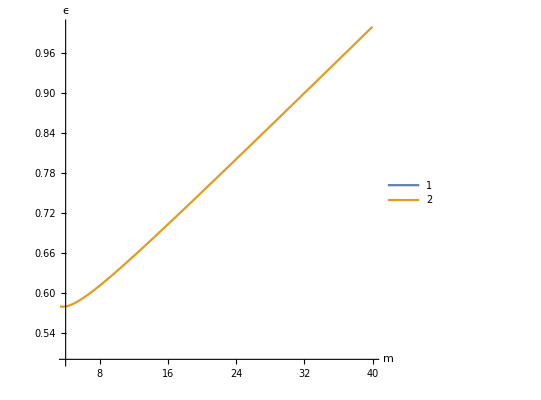

```mathematica
l=1; θ= 0.025; 
Plot[{(2 (√(-l^2 (-1+m) m (-2+m+l m)^2 (-1+θ))+l (-1+m) m (1+θ)+l^2 m (-1+m+θ-m θ)))/(-4+m (3-2 l (-1+θ)+l^2 (-1+θ)+θ)), -(2 (l^2 (-1+m) m (-1+θ)+√(-l^2 (-1+m) m (-2+m+l m)^2 (-1+θ))-l (-1+m) m (1+θ)))/(-4+m (3-2 l (-1+θ)+l^2 (-1+θ)+θ))}, {m, 1, 40}, PlotRange-> {{4,40},{0.5, 1}}, AxesLabel->{m,ϵ}, PlotLegends->Automatic, AspectRatio->1]
```

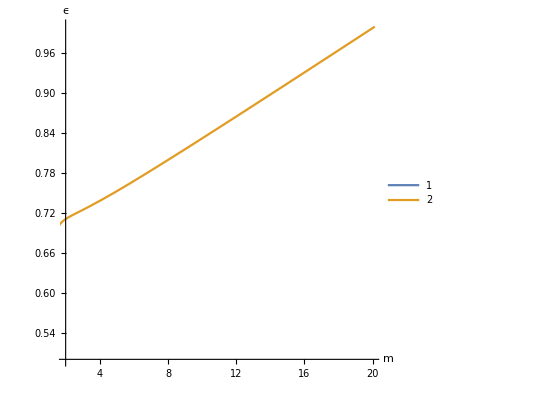

```mathematica
l=2; θ= 0.025; 
Plot[{(2 (√(-l^2 (-1+m) m (-2+m+l m)^2 (-1+θ))+l (-1+m) m (1+θ)+l^2 m (-1+m+θ-m θ)))/(-4+m (3-2 l (-1+θ)+l^2 (-1+θ)+θ)), -(2 (l^2 (-1+m) m (-1+θ)+√(-l^2 (-1+m) m (-2+m+l m)^2 (-1+θ))-l (-1+m) m (1+θ)))/(-4+m (3-2 l (-1+θ)+l^2 (-1+θ)+θ))}, {m, 1, 40}, PlotRange-> {{2,20},{0.5, 1}}, AxesLabel->{m,ϵ}, PlotLegends->Automatic, AspectRatio->1]
```

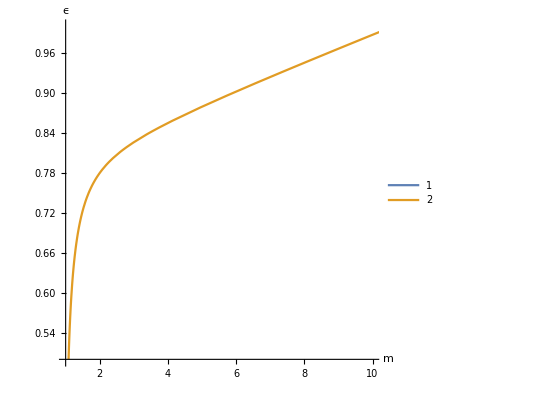

```mathematica
l=4; θ= 0.025; 
Plot[{(2 (√(-l^2 (-1+m) m (-2+m+l m)^2 (-1+θ))+l (-1+m) m (1+θ)+l^2 m (-1+m+θ-m θ)))/(-4+m (3-2 l (-1+θ)+l^2 (-1+θ)+θ)), -(2 (l^2 (-1+m) m (-1+θ)+√(-l^2 (-1+m) m (-2+m+l m)^2 (-1+θ))-l (-1+m) m (1+θ)))/(-4+m (3-2 l (-1+θ)+l^2 (-1+θ)+θ))}, {m, 1, 40}, PlotRange-> {{1,10},{0.5, 1}}, AxesLabel->{m,ϵ}, PlotLegends->Automatic, AspectRatio->1]
```

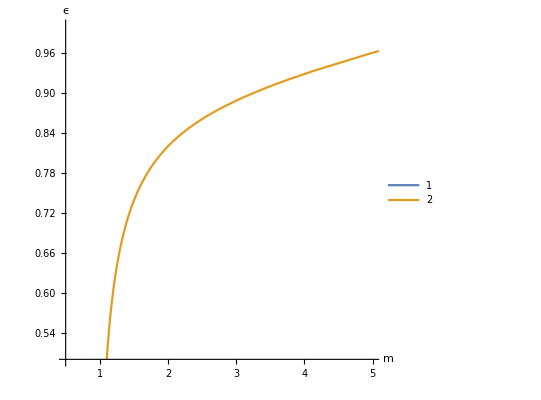

```mathematica
l=8; θ= 0.025; 
Plot[{(2 (√(-l^2 (-1+m) m (-2+m+l m)^2 (-1+θ))+l (-1+m) m (1+θ)+l^2 m (-1+m+θ-m θ)))/(-4+m (3-2 l (-1+θ)+l^2 (-1+θ)+θ)), -(2 (l^2 (-1+m) m (-1+θ)+√(-l^2 (-1+m) m (-2+m+l m)^2 (-1+θ))-l (-1+m) m (1+θ)))/(-4+m (3-2 l (-1+θ)+l^2 (-1+θ)+θ))}, {m, 1, 40}, PlotRange-> {{0.5,5},{0.5, 1}}, AxesLabel->{m,ϵ}, PlotLegends->Automatic, AspectRatio->1]
```

```mathematica
Clear[QRand, QCord, l,θ,ϵ,m]
```